```mathematica
(*График плотности экспоненциальное*)
p1 =Plot[{1*Exp[-1x],2* Exp[-2 x],3* Exp[-3 x],4* Exp[-4 x]},{x,0,2},PlotLegends->Automatic, PlotRange->{{0,2},{0,4}}]
```

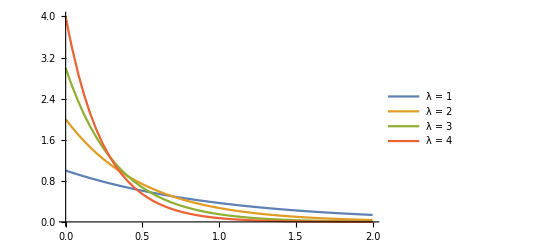

```mathematica
(*График функции распределения экспоненциальное*)
p2 =Plot[{1 - Exp[-1/2 x], 1 - Exp[-1 x],1 - Exp[-2x],1 - Exp[-3x] },{x,0,5},PlotLegends->Automatic ]
```

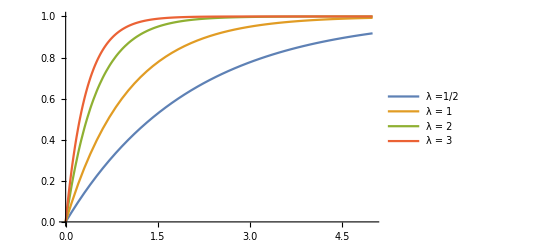

```mathematica
(*Гистограмма вероятностей геометрического*)
p3 = DiscretePlot[Table[PDF[GeometricDistribution[p],k],{p,{0.1,0.2,0.4}}]//Evaluate,{k,15},PlotMarkers->Automatic,PlotRange->All,PlotLegends->Automatic]
```

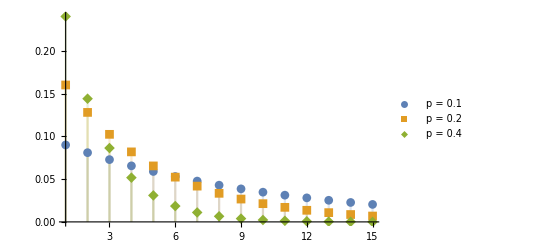

```mathematica
(*График функции распределения геометрического*)
p4 = DiscretePlot[Table[CDF[GeometricDistribution[p],k],{p,{0.1,0.2,0.5}}]//Evaluate,{k,0,14},ExtentSize->Right,PlotLegends->Automatic]
```